### 1. Write a small program for iterating such maps

First Define the function f, and give a value to r, and then generate a nest list, which is the iteration of f.

```mathematica
r = 3.15
```

3.15

```mathematica
f[x_]:= r x (1-x)
```

```mathematica
l1 = NestList[f,0.01,10]
```

{0.01,0.031185,0.0951694,0.271253,0.622676,0.740094,0.605917,0.752162,0.587205,0.763545,0.568714}

#### 2. Write a small program for displaying time series as a trajectory in a ‘return plot’

From the nest list generated above, get points that are on function f

```mathematica
p1 = Partition[l1,2,1]
```

{{0.01,0.031185},{0.031185,0.0951694},{0.0951694,0.271253},{0.271253,0.622676},{0.622676,0.740094},{0.740094,0.605917},{0.605917,0.752162},{0.752162,0.587205},{0.587205,0.763545},{0.763545,0.568714}}

Get points such that x_t+1 = x_t

```mathematica
p2 = l1 /. x_Real ->  {x,x}
```

{{0.01,0.01},{0.031185,0.031185},{0.0951694,0.0951694},{0.271253,0.271253},{0.622676,0.622676},{0.740094,0.740094},{0.605917,0.605917},{0.752162,0.752162},{0.587205,0.587205},{0.763545,0.763545},{0.568714,0.568714}}

```mathematica
pre1 = Prepend[p1,{l1[[1]],0}]
```

{{0.01,0},{0.01,0.031185},{0.031185,0.0951694},{0.0951694,0.271253},{0.271253,0.622676},{0.622676,0.740094},{0.740094,0.605917},{0.605917,0.752162},{0.752162,0.587205},{0.587205,0.763545},{0.763545,0.568714}}

Prepare for the points that are to be plotted

```mathematica
t1 = Thread[{pre1,p2}]
```

{{{0.01,0},{0.01,0.01}},{{0.01,0.031185},{0.031185,0.031185}},{{0.031185,0.0951694},{0.0951694,0.0951694}},{{0.0951694,0.271253},{0.271253,0.271253}},{{0.271253,0.622676},{0.622676,0.622676}},{{0.622676,0.740094},{0.740094,0.740094}},{{0.740094,0.605917},{0.605917,0.605917}},{{0.605917,0.752162},{0.752162,0.752162}},{{0.752162,0.587205},{0.587205,0.587205}},{{0.587205,0.763545},{0.763545,0.763545}},{{0.763545,0.568714},{0.568714,0.568714}}}

```mathematica
f1 = Flatten[t1,1]
```

{{0.01,0},{0.01,0.01},{0.01,0.031185},{0.031185,0.031185},{0.031185,0.0951694},{0.0951694,0.0951694},{0.0951694,0.271253},{0.271253,0.271253},{0.271253,0.622676},{0.622676,0.622676},{0.622676,0.740094},{0.740094,0.740094},{0.740094,0.605917},{0.605917,0.605917},{0.605917,0.752162},{0.752162,0.752162},{0.752162,0.587205},{0.587205,0.587205},{0.587205,0.763545},{0.763545,0.763545},{0.763545,0.568714},{0.568714,0.568714}}

```mathematica
g[y_]:= y
```

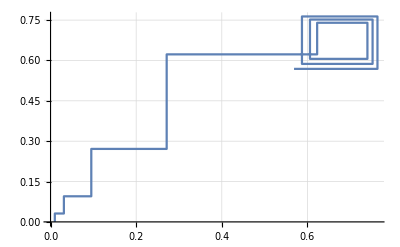

```mathematica
plot1 = ListLinePlot[f1,GridLines->Automatic,Axes-> True]
```

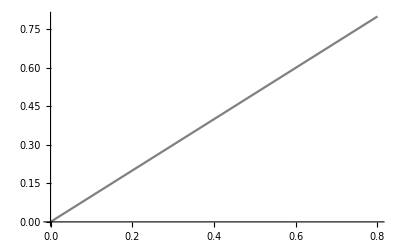

```mathematica
plot2 = Plot[g[x],{x,0,0.8},PlotStyle->Gray]
```

Show the plot of the the iterations

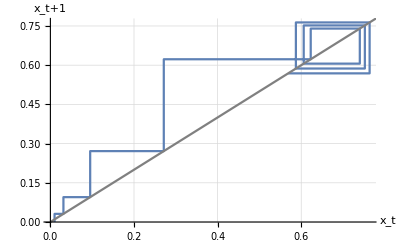

```mathematica
Show[plot1,plot2,AxesLabel -> {x_t,x_t+1}]
```

### Semi-analytically analyze the stability of the period-2 cycle.

Reference: The function insertStability is slightly modified from the lecture notes by the Professor.

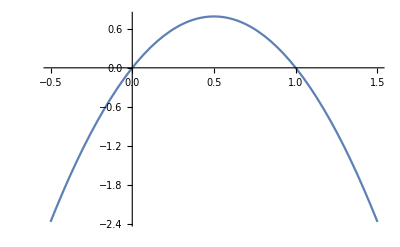

```mathematica
plot11 = Plot[f[x],{x,-0.5,1.5}]
```

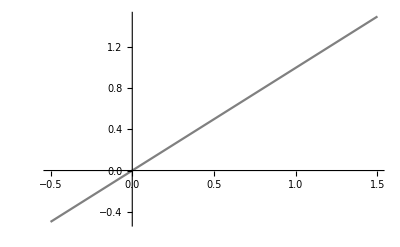

```mathematica
plot22 = Plot[g[x],{x,-0.5,1.5},PlotStyle->Gray]
```

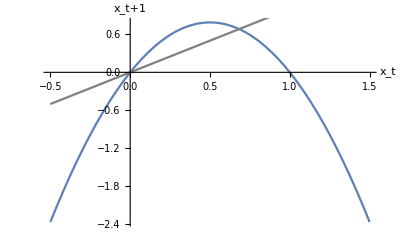

```mathematica
Show[plot11,plot22,AxesLabel -> {x_t,x_t+1}]
```

Find the fixed points for function f

```mathematica
fp = Solve[r x(1-x) == x, x]
```

{{x→0.},{x→0.68254}}

```mathematica
help1 = D[r x(1-x),x]/.fp
```

{3.15,-1.15}

Show the the stable (red) fixed point and unstable (blue) fixed point separately and in the same plot

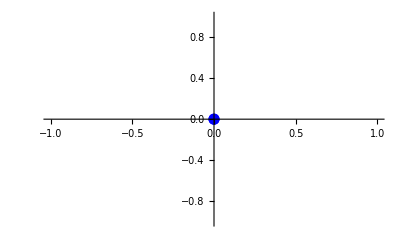
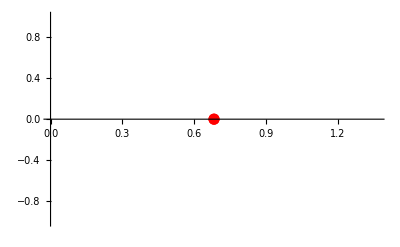

```mathematica
help2 = Table[If[help1[[j]]< 0, ListPlot[{{x /. fp[[j]],0}},PlotStyle->{{AbsolutePointSize[8],Red}}],ListPlot[{{x /. fp[[j]],0}},PlotStyle->{{AbsolutePointSize[8],Blue}}]],{j,1,Length[help1]}]
```

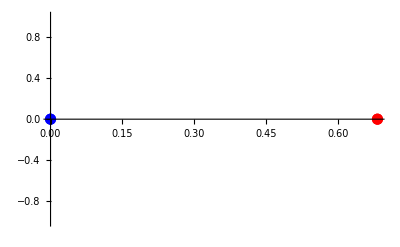

```mathematica
Show[help2,PlotRange->All]
```

Function insertStability will find the stable and unstable fixed points and plot the points on the function

```mathematica
insertStability[fun_,var_,range_]:=Module[{tmp1,tmp2,tmp3,tmp4,tmp5,tmp6},
tmp1 = Solve[ fun==var,var];
tmp2 = D[fun,var]; 
tmp3 = tmp2 /. tmp1;
tmp4 = Table[If[tmp3[[j]]< 0, ListPlot[{{var /. tmp1[[j]],fun /. tmp1[[j]]}},PlotStyle->{{AbsolutePointSize[8],Red}}],ListPlot[{{var /. tmp1[[j]],0}},PlotStyle->{{AbsolutePointSize[8],Blue}}]],{j,1,Length[tmp3]}];
tmp5 = Show[tmp4];
tmp6 = Plot[fun,{var,range[[1]],range[[2]]},PlotStyle->Black,Frame->True];
Show[tmp6,tmp5]]
```

```mathematica
s = insertStability[r x(1-x),x,{-0.5,1.5}]
```

The red point is the stable fixed point, while the blue point is the unstable fixed point.

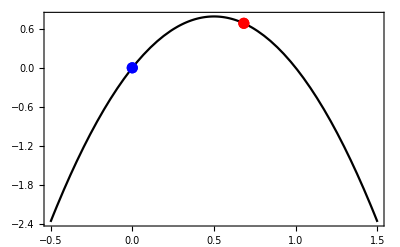

```mathematica
line = ListLinePlot[{{-0.5,-0.5},{1.5,1.5}},PlotStyle->Gray];
```

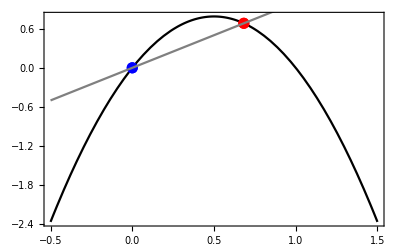

```mathematica
Show[s,line]
```

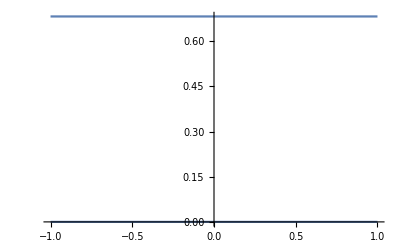

```mathematica
Plot[x /. fp,{r,-1,1}]
```